{{+,+},{neg,neg},{sin,sin},{2,2},{*,*},{pi,π},{3,3}}

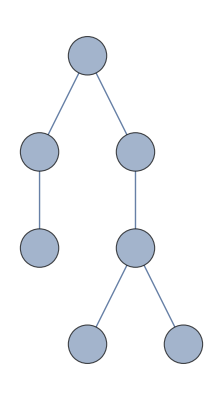

Set::write: Tag Inherited in Inherited["State"] is Protected.

```mathematica
LabelList = {{"+","+"},{"neg","neg"},{"sin","sin"},{"2","2"},{"*","*"},{"pi","π"},{"3","3"}}
TreeGraph[{"+"->"neg","+"->"sin","neg"->"2","sin"->"*","*"->"3","*"->"pi"}, VertexLabels->(#[[1]]->Placed[#[[2]],Center]&/@LabelList),
VertexSize->Large,VertexLabelStyle->Directive[20,FontFamily->"Courier"]]
```